## data & functions

```mathematica
LastPosition[list_,item_,default_:Missing["NotFound"],heuristics_:Infinity]:=Module[{revPos},revPos=FirstPosition[Reverse[list],item,default,heuristics];
If[revPos===default,default,Length[list]+1-revPos]]
```

```mathematica
SparseTimeMovingAverage[data_List,windowSize_?NumericQ]:=Module[{times,values,averageValues,result,halfWindow,timeWindowIndices},(*Extract times and values*){times,values}=Transpose[data];
(*Half of the window size*)halfWindow=windowSize/2;
(*Moving average calculation*)averageValues=Table[(*Find indices of times within the window around the current time point*)timeWindowIndices=Flatten[Position[times,_?(Abs[#-times[[i]]]<=halfWindow&)]];
If[Length[timeWindowIndices]>0,Mean[values[[timeWindowIndices]]],(*Calculate mean if indices are found*)values[[i]] (*Use current value if no other values are in the window*)],{i,Length[times]}];
(*Combine times with calculated averages*)result=Transpose[{times,averageValues}]]
```

```mathematica
NearestPosition[list_,element_]:=Position[list,Nearest[list,element][[1]]][[1]][[1]]
```

```mathematica
NearestPositions[list_,element_]:=Sort[Flatten[Map[Position[list,#]&,Nearest[list,element,2]]]]
```

```mathematica
BoundingPositions[list_,element_]:=If[
Length[Select[list,#<element&]]==0,
{None,None},
Position[list,Last[Select[list,#<element&]]][[1]][[1]]//{#,#+1}&
]
```

```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
roomNames={"ovi","PK","SZGK","Gólyairoda","Mérce","vendégtér","kisterem","trafóház","Oktopusz 1"};
```

```mathematica
startDate=DateObject[{2023,11,9,0,0}];
```

```mathematica
log =Join[
Map[Map[
StringSplit[StringDelete[#,{"{","}","'",",","\t"}],": "]&,
#]&,Import[NotebookDirectory[]<>"log_1.log"]],
Map[Map[
StringSplit[StringDelete[#,{"{","}","'",",","\t"}],": "]&,
#]&,Import[NotebookDirectory[]<>"log.log"]]
];
```

```mathematica
tempControlledRooms={1,2,3,4,5,6,7,9};
```

```mathematica
roomToPump={1,1,2,2,2,3,3,4,1};
```

## basic vis

```mathematica
roomTemps=Map[
Map[#[[{1,3}]]&,#]
&,GatherBy[Map[
{DateObject[#[[1]]],ToExpression[#[[2]]],ToExpression[#[[3]]]}
&,Map[Flatten[#][[{2,4,5}]]&,Transpose[Transpose[Select[log,MemberQ[Flatten[#],"temp measurement"]&]][[{4,3}]]]]
],#[[2]]&]];
```

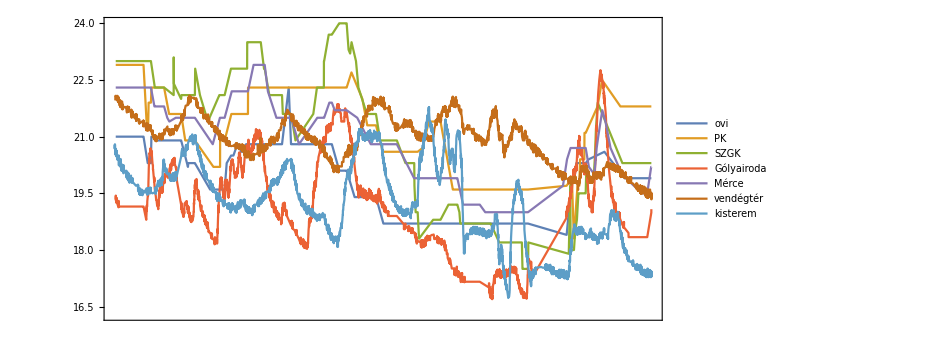

```mathematica
DateListPlot[
Quiet[Table[Select[roomTemps[[room]],startDate<#[[1]]&],{room,1,7}]],PlotLegends->roomNames,
ImageSize->{700,Automatic},AspectRatio->0.5,Joined->True
]
```

```mathematica
roomTempsN=Map[
Map[#[[{1,3}]]&,#]
&,GatherBy[Map[
{DateDifferenceInUnits[startDate,DateObject[#[[1]]],"Minutes"],ToExpression[#[[2]]],ToExpression[#[[3]]]}
&,Map[Flatten[#][[{2,4,5}]]&,Transpose[Transpose[Select[log,MemberQ[Flatten[#],"temp measurement"]&]][[{4,3}]]]]
],#[[2]]&]];
```

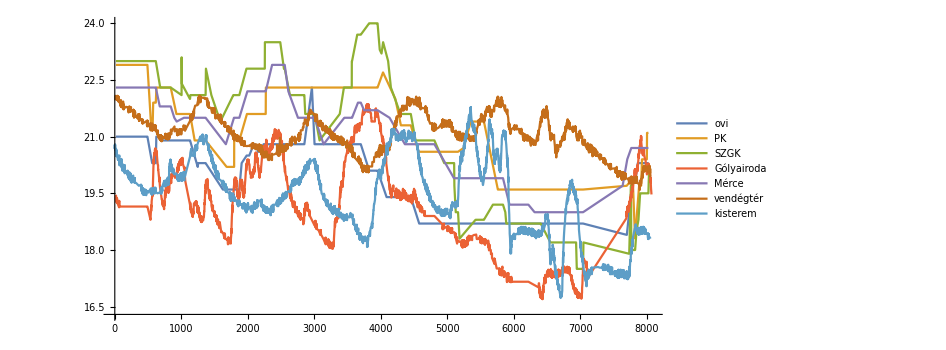

```mathematica
ListPlot[
Quiet[Table[Select[roomTempsN[[room]],0<#[[1]]&],{room,1,7}]],PlotLegends->roomNames,
ImageSize->{700,Automatic},AspectRatio->0.5,Joined->True
]
```

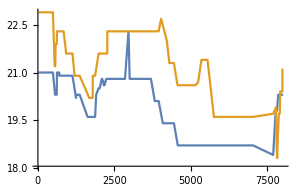
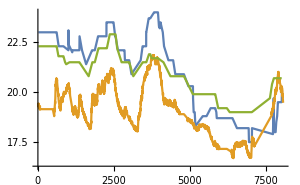
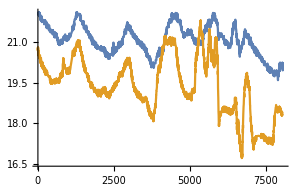

```mathematica
Table[
ListPlot[
Table[
Select[roomTempsN[[room]],0<#[[1]]&]
,{room,{{1,2},{3,4,5},{6,7}}[[cycle]]}],Joined->True,
ImageSize->300
],{cycle,1,3}]
```

```mathematica
sparseData=Select[roomTempsN[[1]],0<#[[1]]&];
noisyData=Select[roomTempsN[[4]],0<#[[1]]&];
```

```mathematica
MinMax[Transpose[sparseData][[1]]]
```

{17,7046.52}

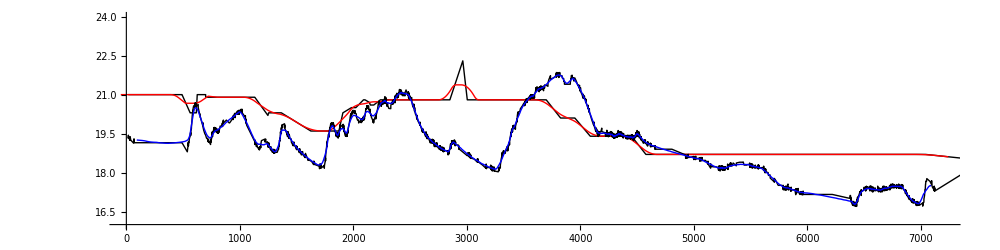

```mathematica
startDay=0;
endDay=5;
smoothedSparseData=MovingAverage[Quiet[Map[{#,Interpolation[sparseData,InterpolationOrder->1][x]/.{x->#}}&,Range[(startDay-0.1) 24 60 ,(endDay+0.1) 24 60,10]]],20];
smoothedNoisyData=MovingAverage[Select[noisyData,Between[#[[1]],{(startDay-0.1) 24 60 ,(endDay+0.1) 24 60}]&],20];
ListPlot[
{
sparseData,
smoothedSparseData,
noisyData,
smoothedNoisyData
},
ImageSize->1000,PlotStyle->{{Thin,Black},{Thick,Red},{Thin,Black},{Thick,Blue}},Joined->True,PlotRange->{{startDay 24 60 ,endDay 24 60},{16,24}},AspectRatio->0.25
]
```

```mathematica
CPUtemps=Map[
{DateObject[#[[1]][[2]]],ToExpression[#[[2]][[3]]]}
&,Transpose[Transpose[Select[log,MemberQ[Flatten[#],"CPU temp"]&]][[{4,3}]]]];
```

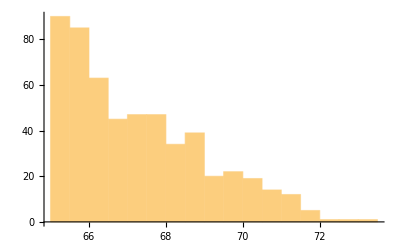

```mathematica
Histogram[Transpose[CPUtemps][[2]]]
```

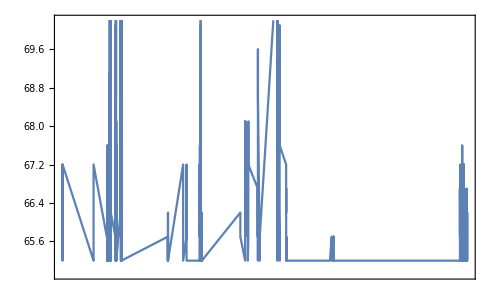

```mathematica
DateListPlot[CPUtemps]
```

```mathematica
cycleOnOff=Map[Map[{#[[1]],#[[3]]}&,#]&,GatherBy[Map[
{DateObject[#[[4]][[2]]],ToExpression[#[[3]][[2]]],Unitize[ToExpression[#[[3]][[3]]]]}
&,Select[log,MemberQ[Flatten[#],"cycle"]&]],#[[2]]&]];
```

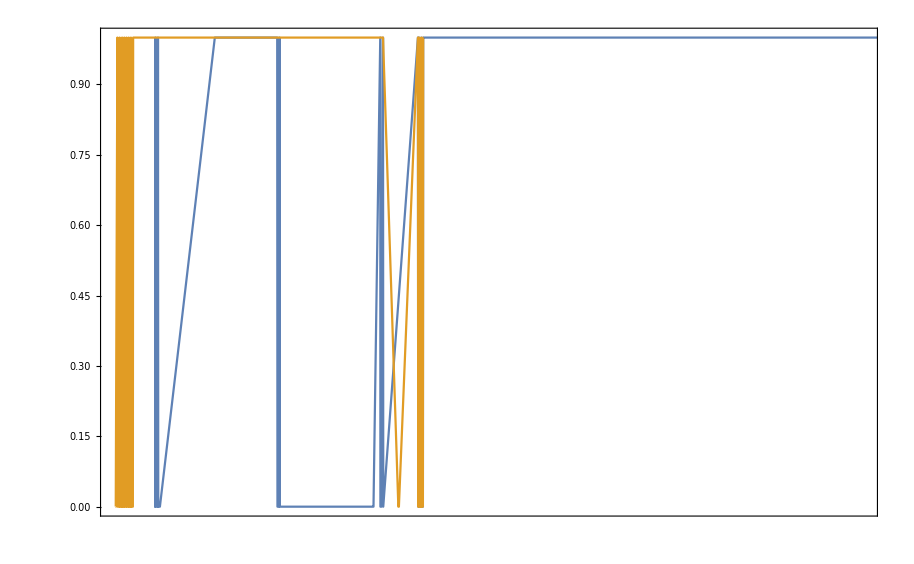

```mathematica
DateListPlot[
{
cycleOnOff[[1]][[-80;;-1]],
cycleOnOff[[2]][[-80;;-1]]
}
]
```

```mathematica
heatingOnoff=Map[
{DateObject[#[[4]][[2]]],ToExpression[#[[3]][[2]]]}
&,Select[log,MemberQ[Flatten[#],"albatros"]&]
];
```

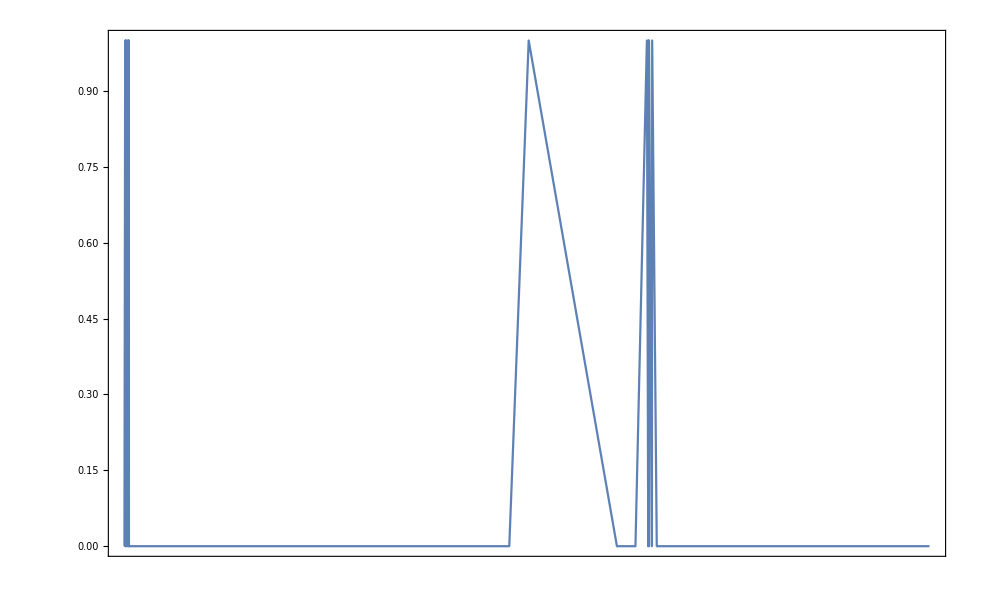

```mathematica
DateListPlot[
heatingOnoff[[-50;;-1]]
]
```

## estimating k-values

```mathematica
Select[log,StringContainsQ[StringRiffle[Flatten[#]],"reachability"]&&StringContainsQ[StringRiffle[Flatten[#]],"False"]&]
```

```mathematica
raspiErrors=Select[log,StringContainsQ[StringRiffle[Flatten[#]],"error"]&&StringContainsQ[StringRiffle[Flatten[#]],"RasPi"]&];
```

```mathematica
timeGranularity ="Hours";
```

```mathematica
roomTemps=Table[Select[list,0<#[[1]]&],{list,Map[
Map[#[[{1,3}]]&,#]
&,GatherBy[Map[
{DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity],ToExpression[#[[2]]],ToExpression[#[[3]]]}
&,Map[Flatten[#][[{2,4,5}]]&,Transpose[Transpose[Select[log,MemberQ[Flatten[#],"temp measurement"]&&MemberQ[Flatten[#],"sensor"]==False&]][[{4,3}]]]]
],#[[2]]&]]}];
```

```mathematica
roomSetTemps=Table[Select[list,0<#[[1]]&],{list,Map[
Map[#[[{1,3}]]&,#]
&,GatherBy[Map[
{DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity],ToExpression[#[[2]]],ToExpression[#[[3]]]}
&,Map[Flatten[#][[{2,4,5}]]&,Transpose[Transpose[Select[log,MemberQ[Flatten[#],"set temp"]&]][[{4,3}]]]]
],#[[2]]&]]}];
```

```mathematica
albatrosState=Select[Map[{
DateDifferenceInUnits[startDate,DateObject[#[[4]][[2]]],timeGranularity],
#[[3]][[2]]
}&,Select[log,#[[1]][[2]]=="state"&&#[[2]][[2]]=="albatros"&]],0<#[[1]]&];
albatrosState=ToExpression[Quiet[Select[
albatrosState,
albatrosState[[Position[albatrosState,#][[1]][[1]]+1]][[2]]!=#[[2]]&
]]];
```

```mathematica
pumpStates=Table[
Select[Transpose[Transpose[list][[{1,3}]]],0<#[[1]]&]
,{list,GatherBy[Map[{
DateDifferenceInUnits[startDate,DateObject[#[[4]][[2]]],timeGranularity],
#[[3]][[2]],
#[[3]][[3]]
}&,Select[log,#[[1]][[2]]=="state"&&#[[2]][[2]]=="pump"&]],#[[2]]&]}];
pumpStates=Table[
ToExpression[Quiet[Select[
list,
list[[Position[list,#][[1]][[1]]+1]][[2]]!=#[[2]]&
]]]
,{list,pumpStates}];
```

```mathematica
externalTemp=Select[ToExpression[Map[
{
DateDifferenceInUnits[startDate,DateObject[#[[4]][[2]]],timeGranularity],
#[[3]][[2]]
}
&,Select[log,#[[2]][[2]]=="external temp"&]]],0<#[[1]]&];
```

```mathematica
smoothedRoomTemps=Table[SparseTimeMovingAverage[roomTemps[[room]],0.5],{room,1,9}];
```

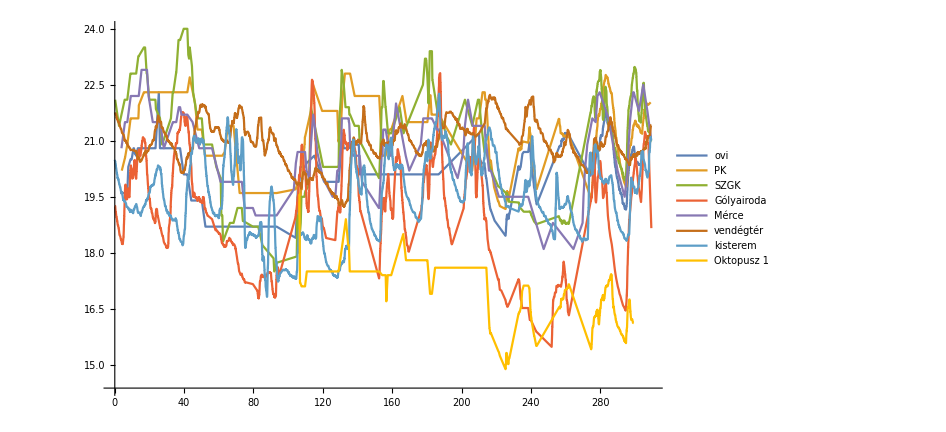

```mathematica
ListPlot[
smoothedRoomTemps[[1;;8]],Joined->True,PlotLegends->roomNames[[{1,2,3,4,5,6,7,9}]],ImageSize->700,PlotRange->{{All,All}}
]
```

```mathematica
log[[-10;;-1]]//Grid
```

{1,state} | {2,override detection} | {3,7} | {4,2023-11-16 11:57:30}
{1,state} | {2,override detection} | {3,7} | {4,2023-11-16 11:58:00}
{1,state} | {2,RasPi} | {3,CPU temp,62.8} | {4,2023-11-16 11:58:01}
{1,state} | {2,override detection} | {3,7} | {4,2023-11-16 11:58:30}
{1,state} | {2,override detection} | {3,7} | {4,2023-11-16 11:59:00}
{1,state} | {2,RasPi} | {3,CPU temp,62.8} | {4,2023-11-16 11:59:00}
{1,state} | {2,override detection} | {3,7} | {4,2023-11-16 11:59:30}
{1,state} | {2,set temp} | {3,7,21.0} | {4,2023-11-16 12:00:00}
{1,state} | {2,external temp} | {3,11.5} | {4,2023-11-16 12:00:00}
{1,state} | {2,RasPi} | {3,CPU temp,62.3} | {4,2023-11-16 12:00:00}

```mathematica
categorizedSmoothedRoomTemps=Table[Table[
Quiet[Module[
{albatrosBounding,pumpBounding},
albatrosBounding=BoundingPositions[Transpose[albatrosState][[1]],dataPoint[[1]]];
pumpBounding=BoundingPositions[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],dataPoint[[1]]];
Flatten[{
If[MemberQ[albatrosBounding,None],-1,albatrosState[[albatrosBounding[[1]]]][[2]]],
If[MemberQ[pumpBounding,None],-1,pumpStates[[roomToPump[[room]]]][[pumpBounding[[1]]]][[2]]],
externalTemp[[NearestPosition[Transpose[externalTemp][[1]],dataPoint[[1]]]]][[2]],
dataPoint
}]
]],{dataPoint,smoothedRoomTemps[[room]]}],{room,1,5}];
```

```mathematica
kEstimates=Table[Map[
Transpose[Transpose[#][[2;;3]]]
&,SortBy[GatherBy[Map[
{#[[3]],#[[8]],#[[9]]}
&,Select[
Map[
Flatten[
{
#[[2]][[1;;2]]-#[[1]][[1;;2]],(*konzisztens-e, amit a fűtöttségi állapotról tudunk; 1-2*)
#[[1]][[1;;2]],(*fűtöttségi állapot az albatros szerint; 3-4*)
#[[2]][[1;;2]],(*fűtöttségi állapot a pumpa szerint; 5-6*)
#[[2]][[5]]-#[[1]][[5]],(*ΔT; 7*)
Mean[Transpose[#][[5]]]-Mean[Transpose[#][[3]]](*T_int - T_ext; 8*),
(#[[2]][[5]]-#[[1]][[5]])/(#[[2]][[4]]-#[[1]][[4]])(*ΔT/Δt; 9*)
}
]&,Drop[Transpose[{categorizedSmoothedRoomTemps[[room]],RotateLeft[categorizedSmoothedRoomTemps[[room]]]}],-1]],
#[[3]]!=-1&&#[[5]]!=-1&&#[[7]]!=0.
&]],First],#[[1]][[1]]&]],{room,1,5}];
```

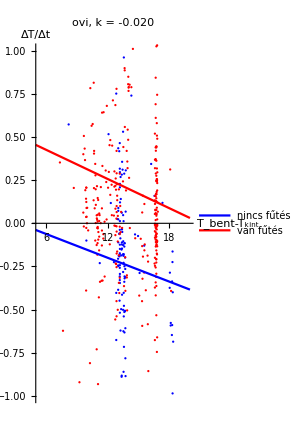
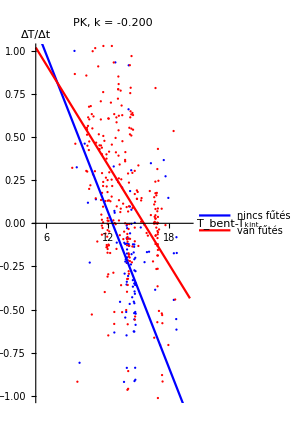
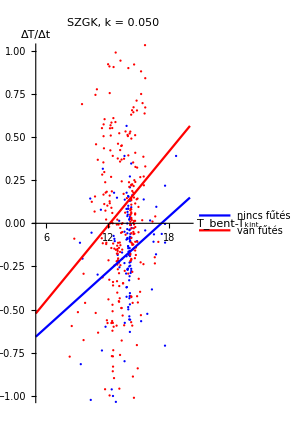
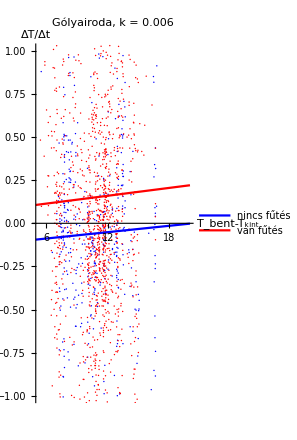
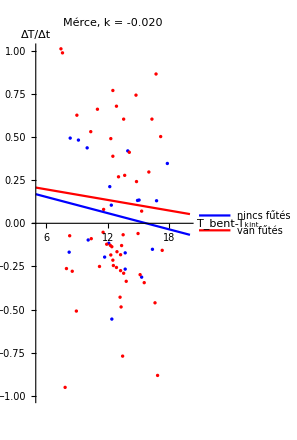

```mathematica
Row[Table[Show[{
ListPlot[
Table[kEstimates[[room]][[onOff]],{onOff,1,2}],PlotLabel->roomNames[[room]]<>", \n"<>ToString[k]<>" = "<>ToString[NumberForm[Evaluate[Table[Fit[kEstimates[[room]][[onOff]],{1,x},x],{onOff,1,2}]][[1]][[2]][[1]],{1,3}]],PlotStyle->{Blue,Red},
ImageSize->220,AxesLabel->{Subscript[T,bent]-Subscript[T,kint],"ΔT/Δt"},AspectRatio->2,PlotRange->{{5,20},{-1,1}}
],
Plot[
Evaluate[Table[Fit[kEstimates[[room]][[onOff]],{1,x},x],{onOff,1,2}]],{x,5,20},
PlotLegends->Placed[{"nincs fűtés","van fűtés"},Bottom],PlotStyle->{Blue,Red}
]
}],{room,1,5}]]
```

## 2 week vis

```mathematica
roomNames={"ovi","PK","SZGK","Gólyairoda","Mérce","vendégtér","kisterem","Oktopusz 1","trafóház"};
```

```mathematica
tStart=Round[Max[Map[Max[Transpose[#][[1]]]&,smoothedRoomTemps]]]-24 3
tEnd=Round[Max[Map[Max[Transpose[#][[1]]]&,smoothedRoomTemps]]]
tStep=1;
```

301

373

```mathematica
Export[NotebookDirectory[]<>"kimutatás.csv",Transpose[{
roomNames[[1;;8]],
Map["hőmérséklet beállított felett: "<>ToString[#]<>"%"&,Round[100roomAboveSetTemp]],
Map["hőmérséklet beállított alatt: "<>ToString[#]<>"%"&,Round[100roomBelowSetTemp]],
Map["fűtöttség egyezik állapottal: "<>ToString[#]<>"%"&,Round[100statusMatchesSettingByRoom]],
Map["fűtünk amikor nem kéne: "<>ToString[#]<>"%"&,Round[100unnecessaryHeatingByRoom]],
Map["nem fűtünk, amikor kéne: "<>ToString[#]<>"%"&,Round[100noHeatingWhenRequestedByRoom]]
}]]
```

Transpose::nmtx: The first two levels of {{ovi,PK,SZGK,Gólyairoda,Mérce,vendégtér,kisterem,trafóház},Round[«54»],«1»,«1»,«1»,Round[«60»]} cannot be transposed.

C:\Users\Beno\Documents\SZAKI\kazankontroll\kimutatás.csv

```mathematica
roomToPump
```

{1,1,2,2,2,3,3,4,1}

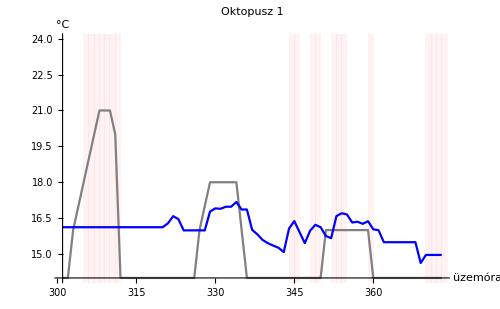
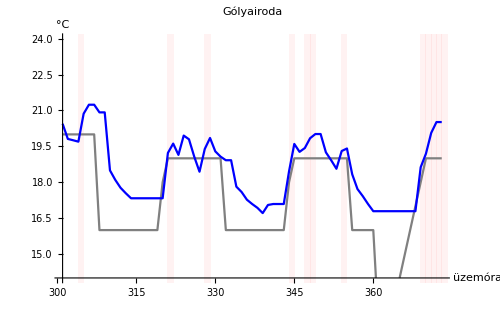
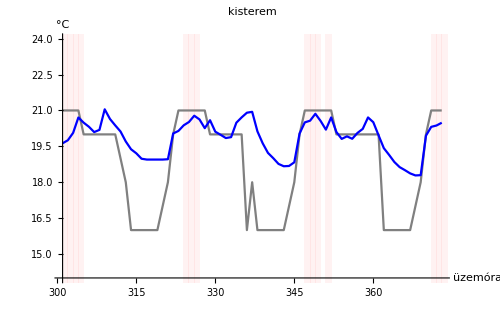
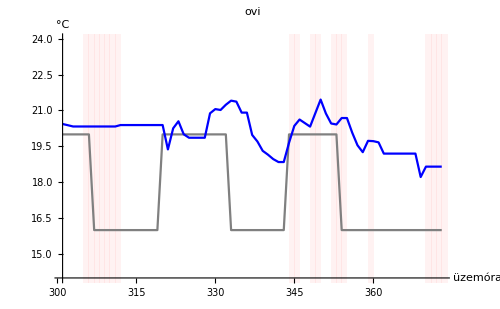
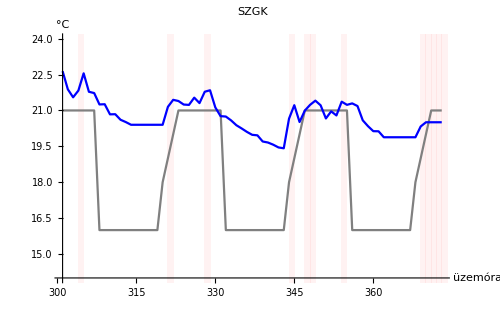
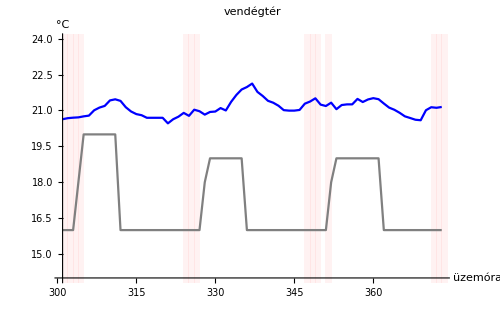
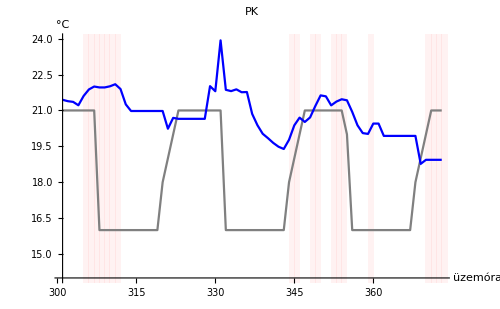
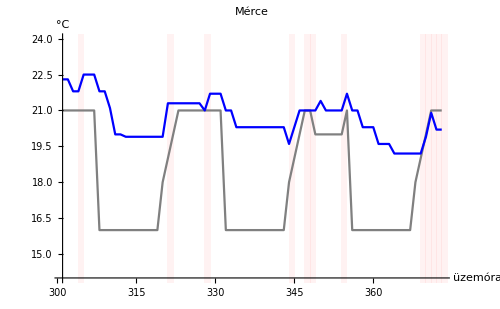
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
roomPlots=ArrayReshape[Quiet[Table[ListPlot[
{
Table[
{t,roomSetTemps[[If[room==8,9,room]]][[PrecedingPos[Transpose[roomSetTemps[[If[room==8,9,room]]]][[1]],t]]][[2]]}
,{t,tStart,tEnd,tStep}],
Table[
{t,smoothedRoomTemps[[room]][[PrecedingPos[Transpose[smoothedRoomTemps[[room]]][[1]],t]]][[2]]}
,{t,tStart,tEnd,tStep}]
},Joined->True,PlotStyle->{Gray,Blue,Blue},PlotLabel->roomNames[[room]],AxesLabel->{"üzemóra","°C"},PlotRange->{{tStart,tEnd},{14,24}},ImageSize->500,
Prolog->{
Map[
If[
#[[2]],
{RGBColor[0,0,1,0],Rectangle[{#[[1]],0},{#[[1]]+tStep,100}]},
{RGBColor[1,0,0,0.05],Rectangle[{#[[1]],0},{#[[1]]+tStep,100}]}
]
&,Quiet[Select[
Table[
{t,pumpStates[[roomToPump[[If[room==8,9,room]]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[If[room==8,9,room]]]]]][[1]],t]]][[2]]==0}
,{t,tStart,tEnd,tStep}],NumberQ[Boole[#[[2]]]]&]]
]
}
],{room,{8,1,2,4,3,5,7,6}}]],{3,3},""]//Transpose//Grid
```

```mathematica
Export[NotebookDirectory[]<>"roomPlots.png",roomPlots]
```

C:\Users\Beno\Documents\SZAKI\kazankontroll\roomPlots.png

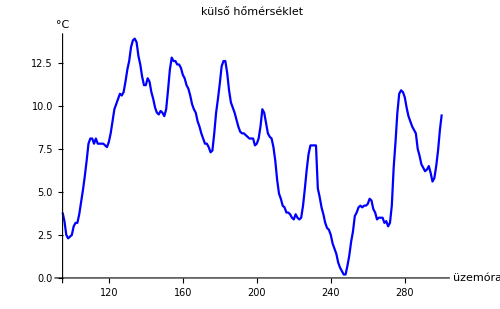
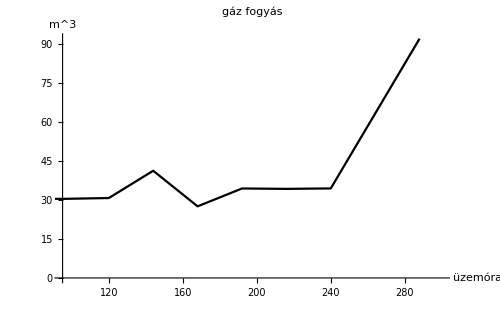

```mathematica
gasAndExt=Row[{ListPlot[
Table[
{t,externalTemp[[PrecedingPos[Transpose[externalTemp][[1]],t]]][[2]]}
,{t,tStart,tEnd,tStep}],Joined->True,PlotStyle->{Blue},PlotLabel->"külső hőmérséklet",AxesLabel->{"üzemóra","°C"},PlotRange->{{95,300},All},ImageSize->500,
Prolog->{
Table[{
If[
albatrosState[[PrecedingPos[Transpose[albatrosState][[1]],t]]][[2]]==0,
RGBColor[0,0,1,0],
RGBColor[1,0,0,0]
],
Rectangle[{t,0},{t+tStep,100}]
}
,{t,tStart,tEnd,tStep}]
}
],
ListPlot[
gas,Joined->True,PlotStyle->Black,PlotLabel->"gáz fogyás",AxesLabel->{"üzemóra","m^3"},PlotRange->{{95,300},All},ImageSize->500,
Prolog->{
Table[{
If[
albatrosState[[PrecedingPos[Transpose[albatrosState][[1]],t]]][[2]]==0,
RGBColor[0,0,1,0],
RGBColor[1,0,0,0]
],
Rectangle[{t,0},{t+tStep,100}]
}
,{t,tStart,tEnd,tStep}]
}
]
}]
```

```mathematica
Export[NotebookDirectory[]<>"gasAndExt.png",gasAndExt]
```

C:\Users\Beno\Documents\SZAKI\kazankontroll\gasAndExt.png

```mathematica
(*mikor megy feleslegesen?*)
(*mikor van, hogy kéne menjen, de nem megy?*)
```

```mathematica
roomAboveSetTemp=Quiet[Table[
N[Total[Select[
Map[
If[
#[[2]]<#[[3]],
1,
0
]
&,Table[
{t,
roomSetTemps[[If[room==8,9,room]]][[PrecedingPos[Transpose[roomSetTemps[[If[room==8,9,room]]]][[1]],t]]][[2]],
smoothedRoomTemps[[room]][[PrecedingPos[Transpose[smoothedRoomTemps[[room]]][[1]],t]]][[2]],
If[pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],t]]][[2]]==1,0,1]
}
,{t,tStart,tEnd,tStep}]],NumberQ]]/((tEnd-tStart+tStep)/tStep)],{room,1,8}]]
```

{0.873786,0.936893,0.936893,0.771845,0.927184,0.990291,0.694175,0.621359}

```mathematica
roomBelowSetTemp=Quiet[Table[
N[Total[Select[
Map[
If[
#[[2]]>#[[3]],
1,
0
]
&,Table[
{t,
roomSetTemps[[If[room==8,9,room]]][[PrecedingPos[Transpose[roomSetTemps[[If[room==8,9,room]]]][[1]],t]]][[2]],
smoothedRoomTemps[[room]][[PrecedingPos[Transpose[smoothedRoomTemps[[room]]][[1]],t]]][[2]],
If[pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],t]]][[2]]==1,0,1]
}
,{t,tStart,tEnd,tStep}]],NumberQ]]/((tEnd-tStart+tStep)/tStep)],{room,1,8}]]
```

{0.126214,0.0631068,0.0631068,0.223301,0.0631068,0.00970874,0.305825,0.320388}

```mathematica
unnecessaryHeatingByRoom=Quiet[Table[
N[Total[Select[
Map[
If[
#[[2]]+1<#[[3]]&&#[[4]]==1,
1,
0
]
&,Table[
{t,
roomSetTemps[[If[room==8,9,room]]][[PrecedingPos[Transpose[roomSetTemps[[If[room==8,9,room]]]][[1]],t]]][[2]],
smoothedRoomTemps[[room]][[PrecedingPos[Transpose[smoothedRoomTemps[[room]]][[1]],t]]][[2]],
If[pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],t]]][[2]]==1,0,1]
}
,{t,tStart,tEnd,tStep}]],NumberQ]]/((tEnd-tStart+tStep)/tStep)],{room,1,8}]]
```

{0.529126,0.558252,0.708738,0.432039,0.640777,0.660194,0.378641,0.461165}

```mathematica
statusMatchesSettingByRoom=Quiet[Table[
N[Total[Select[
Map[
If[
#[[2]]>#[[3]]-1&&#[[4]]==1||#[[2]]<#[[3]]+1&&#[[4]]==0,
1,
0
]
&,Table[
{t,
roomSetTemps[[If[room==8,9,room]]][[PrecedingPos[Transpose[roomSetTemps[[If[room==8,9,room]]]][[1]],t]]][[2]],
smoothedRoomTemps[[room]][[PrecedingPos[Transpose[smoothedRoomTemps[[room]]][[1]],t]]][[2]],
If[pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],t]]][[2]]==1,0,1]
}
,{t,tStart,tEnd,tStep}]],NumberQ]]/((tEnd-tStart+tStep)/tStep)],{room,1,8}]]
```

{0.461165,0.436893,0.271845,0.529126,0.354369,0.145631,0.402913,0.325243}

```mathematica
noHeatingWhenRequestedByRoom=Quiet[Table[
N[Total[Select[
Map[
If[
#[[2]]>#[[3]]-1&&#[[4]]==0,
1,
0
]
&,Table[
{t,
roomSetTemps[[If[room==8,9,room]]][[PrecedingPos[Transpose[roomSetTemps[[If[room==8,9,room]]]][[1]],t]]][[2]],
smoothedRoomTemps[[room]][[PrecedingPos[Transpose[smoothedRoomTemps[[room]]][[1]],t]]][[2]],
If[pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],t]]][[2]]==1,0,1]
}
,{t,tStart,tEnd,tStep}]],NumberQ]]/((tEnd-tStart+tStep)/tStep)],{room,1,8}]]
```

{0.116505,0.0825243,0.0631068,0.160194,0.0873786,0.00485437,0.0728155,0.038835}

```mathematica
{
roomNames,
roomAboveSetTemp,
roomBelowSetTemp,
statusMatchesSettingByRoom,
unnecessaryHeatingByRoom,
noHeatingWhenRequestedByRoom
}
```

{{ovi,PK,SZGK,Gólyairoda,Mérce,vendégtér,kisterem,Oktopusz 1,trafóház},{0.873786,0.936893,0.936893,0.771845,0.927184,0.990291,0.694175,0.621359},{0.126214,0.0631068,0.0631068,0.223301,0.0631068,0.00970874,0.305825,0.320388},{0.300971,0.305825,0.194175,0.169903,0.179612,0.0728155,0.213592,0.286408},{0.640777,0.669903,0.786408,0.713592,0.786408,0.73301,0.533981,0.495146},{0.0582524,0.0242718,0.0194175,0.11165,0.0242718,0.,0.0582524,0.0194175}}